```mathematica
CircleTimes=KroneckerProduct;
$Assumptions=Element[{θ,ϕ}, Reals];
```

```mathematica
a={{0,1},{0,0}};
ad={{0,0},{1,0}};
I2 = IdentityMatrix[2];
```

```mathematica
UBS={{Exp[ⅈ ϕ]Cos[θ], -Sin[θ]},{Exp[ⅈ ϕ]Sin[θ],Cos[θ]}};
LogUBS =-ⅈ MatrixLog[UBS];
```

```mathematica
H=LogUBS[[1,1]] (ad.a)⊗I2 + LogUBS[[1,2]](ad⊗a) + LogUBS[[2,1]](a⊗ad)+LogUBS[[2,2]](I2⊗(ad.a));
```

```mathematica
M=MatrixExp[ⅈ H];
```

```mathematica
bigM=(M⊗M)/.{θ->0.1,ϕ->0.1};
```

```mathematica
(*UBS anc*)
```

```mathematica
UBS…anc={{Exp[ⅈ ϕ]Cos[θ], -Sin[θ],0,0},{Exp[ⅈ ϕ]Sin[θ],Cos[θ],0,0},{0,0,Exp[ⅈ ϕ]Cos[θ], -Sin[θ]},{0,0,Exp[ⅈ ϕ]Sin[θ],Cos[θ]}};
```

```mathematica
LogUBS…anc=-ⅈ MatrixLog[UBS…anc];
```

```mathematica
H…anc=LogUBS…anc[[1,1]] (ad.a)⊗I2⊗I2⊗I2 + 
LogUBS…anc[[1,2]] ad⊗a⊗I2⊗I2+
LogUBS…anc[[2,1]] a⊗ad⊗I2⊗I2+
LogUBS…anc[[2,2]] I2⊗(ad.a)⊗I2⊗I2+
LogUBS…anc[[3,3]] I2⊗I2⊗(ad.a)⊗I2+
LogUBS…anc[[3,4]] I2⊗I2⊗ad⊗a +
LogUBS…anc[[4,3]] I2⊗I2⊗a⊗ad+
LogUBS…anc[[4,4]] I2⊗I2⊗I2⊗(ad.a);
```

```mathematica
M…anc=MatrixExp[ⅈ H…anc];
```

```mathematica
big…anc=M…anc/.{θ->0.1,ϕ->0.1};
```

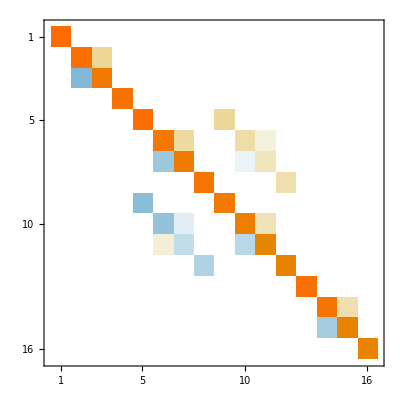

```mathematica
MatrixPlot[big…anc]
```

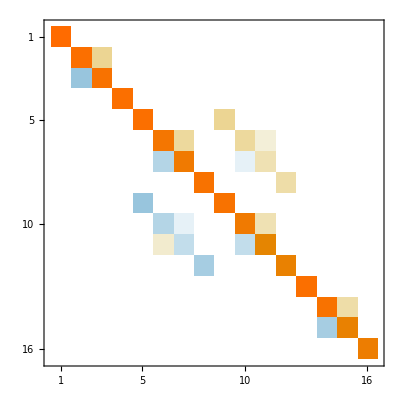

```mathematica
MatrixPlot[bigM]
```

```mathematica
bigM//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.995004-4.30211×10^-16 ⅈ | 0.0993347+0.00996671 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -0.0998334+1.11022×10^-16 ⅈ | 0.990033+0.0993347 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.995004+0.0998334 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.995004-4.30211×10^-16 ⅈ | 0 | 0 | 0 | 0.0993347+0.00996671 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.990033-8.56124×10^-16 ⅈ | 0.0988384+0.00991692 ⅈ | 0 | 0 | 0.0988384+0.00991692 ⅈ | 0.00976804+0.00198008 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.0993347+1.53417×10^-16 ⅈ | 0.985087+0.0988384 ⅈ | 0 | 0 | -0.00991692-0.000995011 ⅈ | 0.0973546+0.0197348 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.990033+0.0993347 ⅈ | 0 | 0 | 0 | 0.0978434+0.0198338 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.0998334+1.11022×10^-16 ⅈ | 0 | 0 | 0 | 0.990033+0.0993347 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.0993347+1.53417×10^-16 ⅈ | -0.00991692-0.000995011 ⅈ | 0 | 0 | 0.985087+0.0988384 ⅈ | 0.0973546+0.0197348 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.00996671-2.21675×10^-17 ⅈ | -0.0988384-0.00991692 ⅈ | 0 | 0 | -0.0988384-0.00991692 ⅈ | 0.970299+0.196689 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0993347-0.00996671 ⅈ | 0 | 0 | 0 | 0.97517+0.197677 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.995004+0.0998334 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.990033+0.0993347 ⅈ | 0.0978434+0.0198338 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0993347-0.00996671 ⅈ | 0.97517+0.197677 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.980067+0.198669 ⅈ)

```mathematica
big…anc//MatrixForm
```

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.995004-1.71391×10^-15 ⅈ | 0.0993347+0.00996671 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -0.0998334-1.7375×10^-14 ⅈ | 0.990033+0.0993347 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.995004+0.0998334 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.995004-1.71391×10^-15 ⅈ | 0 | 0 | 0 | 0.0993347+0.00996671 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.990033+5.20417×10^-17 ⅈ | 0.0988384+0.00991692 ⅈ | 0 | 0 | 0.0988384+0.00991692 ⅈ | 0.00976804+0.00198008 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.0993347+5.55112×10^-17 ⅈ | 0.985087+0.0988384 ⅈ | 0 | 0 | -0.00991692-0.000995011 ⅈ | 0.0973546+0.0197348 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.990033+0.0993347 ⅈ | 0 | 0 | 0 | 0.0978434+0.0198338 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.0998334-1.72085×10^-14 ⅈ | 0 | 0 | 0 | 0.990033+0.0993347 ⅈ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.0993347-2.77556×10^-17 ⅈ | -0.00991692-0.000995011 ⅈ | 0 | 0 | 0.985087+0.0988384 ⅈ | 0.0973546+0.0197348 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.00996671+1.6237×10^-15 ⅈ | -0.0988384-0.00991692 ⅈ | 0 | 0 | -0.0988384-0.00991692 ⅈ | 0.970299+0.196689 ⅈ | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0993347-0.00996671 ⅈ | 0 | 0 | 0 | 0.97517+0.197677 ⅈ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.995004+0.0998334 ⅈ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.990033+0.0993347 ⅈ | 0.0978434+0.0198338 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.0993347-0.00996671 ⅈ | 0.97517+0.197677 ⅈ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.980067+0.198669 ⅈ)

```mathematica
bigM==big…anc
```

False

```mathematica
(*These two matrice are actually identical up to machine point error*)
```